-108.55+0.00113679 y

-5.13494+0.0001174 y+6.03912×10^-10 y^2

-1.40767+0.0000152309 y+7.89524×10^-10 y^2-6.82285×10^-17 y^3

7.34056-0.000400925 y+2.35585×10^-9 y^2-1.76108×10^-15 y^3+5.06409×10^-22 y^4

0.42113-0.000104528 y+3.68568×10^-9 y^2-3.03438×10^-14 y^3+1.42669×10^-19 y^4-3.43268×10^-25 y^5+4.27728×10^-31 y^6-2.55327×10^-37 y^7+5.5625×10^-44 y^8

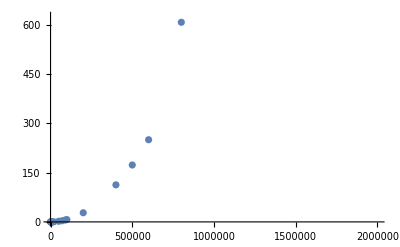

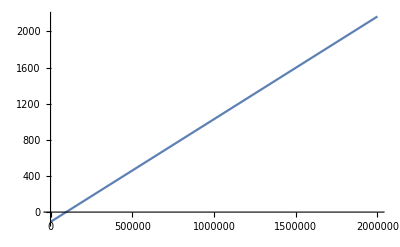

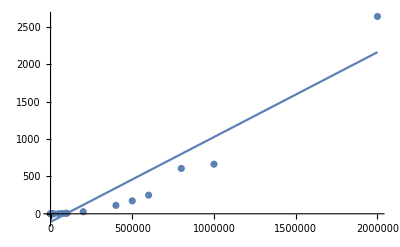

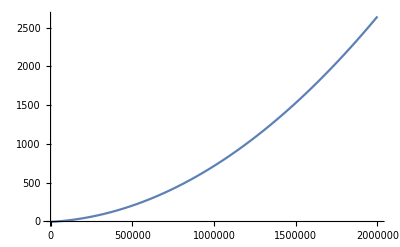

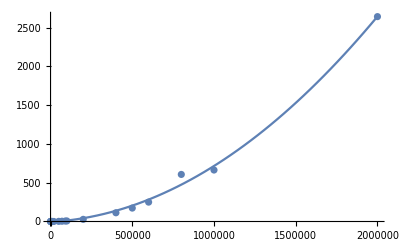

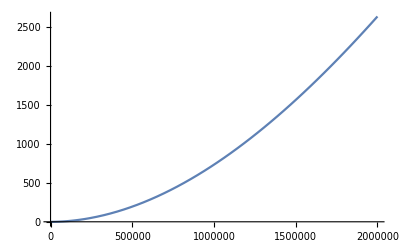

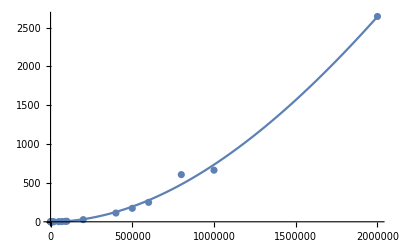

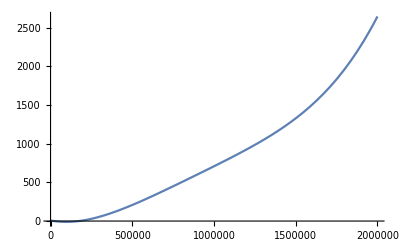

```mathematica
Insercion1=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,y},y]

Insercion2=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,y,y^2},y]

Insercion3=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,y,y^2,y^3},y]

Insercion4=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,y,y^2,y^3,y^4},y]

Insercion8=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,y,y^2,y^3,y^4,y^5,y^6,y^7,y^8},y]

puntos=ListPlot[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}}]

g1=Plot[Insercion1,{y,0,2000000}]
Show[puntos,g1,PlotRange->All]

g2=Plot[Insercion2,{y,0,2000000}]
Show[puntos,g2,PlotRange->All]

g3=Plot[Insercion3,{y,0,2000000}]
Show[puntos,g3,PlotRange->All]

g4=Plot[Insercion4,{y,0,2000000}]
Show[puntos,g4,PlotRange->All]

g8=Plot[Insercion8,{y,0,2000000}]
Show[puntos,g8,PlotRange->All]
```